```mathematica
States[EN_,V_,ORDER_:1]:=Module[{U,N},
N=Length[EN];
U=IdentityMatrix[N];
If[ORDER>=1,U+=Table[If[Subscript[k, 1]!=n,If[PossibleZeroQ[V[[Subscript[k, 1],n]]],0,V[[Subscript[k, 1],n]]/(EN[[n]]-EN[[Subscript[k, 1]]])],0],{Subscript[k, 1],N},{n,N}]];
If[ORDER>=2,U+=Table[If[Subscript[k, 1]!=n,Sum[If[PossibleZeroQ[V[
[Subscript[k, 1],Subscript[k, 2]]]*V[[Subscript[k, 2],n]]],0,(V[
[Subscript[k, 1],Subscript[k, 2]]]*V[[Subscript[k, 2],n]])/((EN[[n]]-EN[[Subscript[k, 1]]])*(EN[[n]]-EN[[Subscript[k, 2]]]))],{Subscript[k, 2],Complement[Range[N],{n}]}]-If[PossibleZeroQ[V[[n,n]]*V[[Subscript[k, 1],n]]],0,(V[[n,n]]*V[[Subscript[k, 1],n]])/(EN[[n]]-EN[[Subscript[k, 1]]])^2],0],{Subscript[k, 1],N},{n,N}]+DiagonalMatrix[Table[Sum[-(1/2)*If[PossibleZeroQ[V[[n,Subscript[k, 1]]]*V[[Subscript[k, 1],n]]],0,(V[[n,Subscript[k, 1]]]*V[[Subscript[k, 1],n]])/(EN[[Subscript[k, 1]]]-EN[[n]])^2],{Subscript[k, 1],Complement[Range[N],{n}]}],{n,N}]]];
If[ORDER>=3,U+=Table[If[Subscript[k, 1]!=n,Sum[-Sum[If[PossibleZeroQ[V[[Subscript[k, 1],Subscript[k, 2]]]*V[[Subscript[k, 2],Subscript[k, 3]]]*V[[Subscript[k, 3],n]]],0,(V[[Subscript[k, 1],Subscript[k, 2]]]*V[[Subscript[k, 2],Subscript[k, 3]]]*V[[Subscript[k, 3],n]])/((EN[[Subscript[k, 1]]]-EN[[n]])*(EN[[n]]-EN[[Subscript[k, 2]]])*(EN[[n]]-EN[[Subscript[k, 3]]]))],{Subscript[k, 3],Complement[Range[N],{n}]}]If[PossibleZeroQ[V[[n,Subscript[k, 2]]]*V[[Subscript[k, 2],n]]*V[[Subscript[k, 1],n]]],0,(V[[n,Subscript[k, 2]]]*V[[Subscript[k, 2],n]]*V[[Subscript[k, 1],n]])/((EN[[Subscript[k, 1]]]-EN[[n]])*(EN[[n]]-EN[[Subscript[k, 2]]]))*(1/(EN[[n]]-EN[[Subscript[k, 1]]])+1/(2(EN[[n]]-EN[[Subscript[k, 2]]])))]+If[PossibleZeroQ[V[[n,n]]*V[[Subscript[k, 1],Subscript[k, 2]]]*V[[Subscript[k, 2],n]]],0,(V[[n,n]]*V[[Subscript[k, 1],Subscript[k, 2]]]*V[[Subscript[k, 2],n]])/((EN[[Subscript[k, 1]]]-EN[[n]])*(EN[[n]]-EN[[Subscript[k, 2]]]))*(1/(EN[[n]]-EN[[Subscript[k, 1]]])+1/(EN[[n]]-EN[[Subscript[k, 2]]]))],{Subscript[k, 2],Complement[Range[N],{n}]}]-If[PossibleZeroQ[V[[n,n]]^2*V[[Subscript[k, 1],n]]],0,(V[[n,n]]^2*V[[Subscript[k, 1],n]])/(EN[[Subscript[k, 1]]]-EN[[n]])^3],0],{Subscript[k, 1],N},{n,N}]+DiagonalMatrix[Table[Sum[-Sum[If[PossibleZeroQ[V[[n,Subscript[k, 2]]]*V[[Subscript[k, 2],Subscript[k, 1]]]*V[[Subscript[k, 1],n]]+V[[Subscript[k, 2],n]]*V[[Subscript[k, 1],Subscript[k, 2]]]*V[[n,Subscript[k, 1]]]],0,(V[[n,Subscript[k, 2]]]*V[[Subscript[k, 2],Subscript[k, 1]]]*V[[Subscript[k, 1],n]]+V[[Subscript[k, 2],n]]*V[[Subscript[k, 1],Subscript[k, 2]]]*V[[n,Subscript[k, 1]]])/(2(EN[[n]]-EN[[Subscript[k, 2]]])^2*(EN[[n]]-EN[[Subscript[k, 1]]]))],{Subscript[k, 2],Complement[Range[N],{n}]}]+If[PossibleZeroQ[V[[n,Subscript[k, 1]]]*V[[Subscript[k, 1],n]]*V[[n,n]]],0,(V[[n,Subscript[k, 1]]]*V[[Subscript[k, 1],n]]*V[[n,n]])/(EN[[n]]-EN[[Subscript[k, 1]]])^3],{Subscript[k, 1],Complement[Range[N],{n}]
}],{n,N}]]];
U
];
```

```mathematica
ρ[T_,H_,R_,h1_,h2_,subNum_]:=Module[{En,hn1,hn2,Ω,Γsquared,Cab,ρ0,rho,rhoNoNoise,J},
En=Diagonal[Inverse[R].H.R]//.subNum;
Ω=Table[En[[j]]-En[[k]],{j,4},{k,4}]*2π//.subNum;
hn1=Diagonal[Inverse[R].h1.R]*2π//.subNum;
hn2=Diagonal[Inverse[R].h2.R]*2π//.subNum;
Γsquared=Table[hn1[[j]]-hn1[[k]],{j,4},{k,4}]^2+Table[hn2[[j]]-hn2[[k]],{j,4},{k,4}]^2//.subNum;
J[t_]:=(2-EulerGamma-Log[2π*10^-9*t])/(2*Log[10^12])*t^2;
ρ0=({{0, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
Cab[a_,b_]:=KroneckerProduct[R[[a,;;]],Transpose[Inverse[R]][[b,;;]]]*(Inverse[R].ρ0.R)//.subNum;
rhoNoNoise=Diagonal[Table[Total[Cab[j,k]*Exp[-I*Ω*t],2],{j,4},{k,4}]]//.subNum;
rho=Diagonal[Table[Total[Cab[j,k]*Exp[-I*Ω*t]*Exp[-J[t]*Γsquared],2],{j,4},{k,4}]]//.subNum;
(*Print["h1= ",h1//.subNum//N//ScientificForm];*)
(*Print["h1= ",h2//.subNum//N//ScientificForm];*)
(*Print["hn1= ",hn1//ScientificForm];*)
(*Print["hn1= ",hn2//ScientificForm];*)
(*Print["H= ",H//.subNum//N//ScientificForm];*)
(*Print["EN= ",En//ScientificForm];*)
(*Print["R= ",R//.subNum//N//ScientificForm];*)
(*Print[Ω];*)
p1=Plot[Evaluate@(rhoNoNoise),{t,0,T},Frame->True,GridLines->Automatic,ImageSize->Large];
p2=Plot[Evaluate@(rho),{t,0,T},Frame->True,GridLines->Automatic,ImageSize->Large];
Grid[{p1,p2}]
]
```

```mathematica
R=States[{-δ,0,δ},({{0, √2 gf*√n0, 0}, {√2 gf*√n0, 0, √2 gf*√(n0-1)}, {0, √2 gf*√(n0-1), 0}}),3]
```

(1-(gf^2 n0)/δ^2 | (√2 gf √n0)/δ | (gf^2 √(n0-1) √n0)/δ^2
-(√2 gf √n0)/δ | -(gf^2 (n0-1))/δ^2-(gf^2 n0)/δ^2+1 | (√2 gf √(n0-1))/δ
(gf^2 √(n0-1) √n0)/δ^2 | -(√2 gf √(n0-1))/δ | 1-(gf^2 (n0-1))/δ^2)

```mathematica
({{1, 0, 0, 0}, {0, 1/√2, 1/√2, 0}, {0, -1/√2, 1/√2, 0}, {0, 0, 0, 1}}).({{1-(gf^2 n0)/δ^2, 0, (√2 gf √n0)/δ, (gf^2 √(n0-1) √n0)/δ^2}, {0, 1, 0, 0}, {-(√2 gf √n0)/δ, 0, -(gf^2 (n0-1))/δ^2-(gf^2 n0)/δ^2+1, (√2 gf √(n0-1))/δ}, {(gf^2 √(n0-1) √n0)/δ^2, 0, -(√2 gf √(n0-1))/δ, 1-(gf^2 (n0-1))/δ^2}})//Simplify
```

(1-(gf^2 n0)/δ^2 | 0 | (√2 gf √n0)/δ | (gf^2 √(n0-1) √n0)/δ^2
-(gf √n0)/δ | 1/(√2) | (δ^2+gf^2 (1-2 n0))/(√2 δ^2) | (gf √(n0-1))/δ
-(gf √n0)/δ | -1/(√2) | (δ^2+gf^2 (1-2 n0))/(√2 δ^2) | (gf √(n0-1))/δ
(gf^2 √(n0-1) √n0)/δ^2 | 0 | -(√2 gf √(n0-1))/δ | 1-(gf^2 (n0-1))/δ^2)

```mathematica
H=({{-δ, gf*√n0, gf*√n0, 0}, {gf*√n0, 0, 0, gf*√(n0-1)}, {gf*√n0, 0, 0, gf*√(n0-1)}, {0, gf*√(n0-1), gf*√(n0-1), δ}});
R=(*({{Cos[ϕ]/√2, 0, -Sin[ϕ], Cos[ϕ]/√2}, {-1/2, 1/√2, 0, 1/2}, {-1/2, -1/√2, 0, 1/2}, {Sin[ϕ]/√2, 0, Cos[ϕ], Sin[ϕ]/√2}});*)({{1, 0, (√2 gf √n0)/δ, 0}, {-(gf √n0)/δ, 1/(√2), 1/(√2), (gf √(n0-1))/δ}, {-(gf √n0)/δ, -1/(√2), 1/(√2), (gf √(n0-1))/δ}, {0, 0, -(√2 gf √(n0-1))/δ, 1}});(*({{1-(gf^2 n0)/δ^2, 0, (√2 gf √n0)/δ, (gf^2 √(n0-1) √n0)/δ^2}, {-(gf √n0)/δ, 1/(√2), (δ^2+gf^2 (1-2 n0))/(√2 δ^2), (gf √(n0-1))/δ}, {-(gf √n0)/δ, -1/(√2), (δ^2+gf^2 (1-2 n0))/(√2 δ^2), (gf √(n0-1))/δ}, {(gf^2 √(n0-1) √n0)/δ^2, 0, -(√2 gf √(n0-1))/δ, 1-(gf^2 (n0-1))/δ^2}});*)
h1=({{w03+w30+w33-2*dzz*n0, 0, -gc*√n0*wp/dc, 0}, {0, w03+w30+w33-2dzz*(n0-1), -dxy, -gc*√(n0-1)*wp/dc}, {-gc*√n0*wp/dc, -dxy, -w03+w30-w33-2dzz*(n0-1)-2dxy, 0}, {0, -gc*√(n0-1)*wp/dc, 0, -w03+w30-w33-2dxy(n0-1)-2dzz(n0-1)}});
h2=({{w03+w30+w33-2*dzz*n0, -gc*√n0*wp/dc, 0, 0}, {-gc*√n0*wp/dc, -w03+w30-w33-2dzz*(n0-1)-2dxy, -dxy, 0}, {0, -dxy, w03+w30+w33-2dzz*(n0-1), -gc*√(n0-1)*wp/dc}, {0, 0, -gc*√(n0-1)*wp/dc, -w03+w30-w33-2dxy(n0-1)-2dzz(n0-1)}});
sub={δ->df+dd,df-> wf-wcav,dc-> wc-wcav,dd->2 gc^2/dc,dzz-> 2 gc^2/dc^2*(w30+w33),dxy-> (gc*gf*wp)/(dc*(dc-df)),ϕ-> ArcTan[√n0,√(n0-1)], wf->10.3,wc->11.4,wcav->10.808452405257746,gc->0.05,n0->4,gf->0.005,wp-> 0.002,w30->0,w33->0,w03->0};
approx={w03->0,w30->0,w33->0,dzz->0,dxy->0};
Print[{df,dc,dd,dzz,dxy,wp}//.sub]
```

{-0.508452,0.591548,0.00845241,0.,7.684×10^-7,0.002}

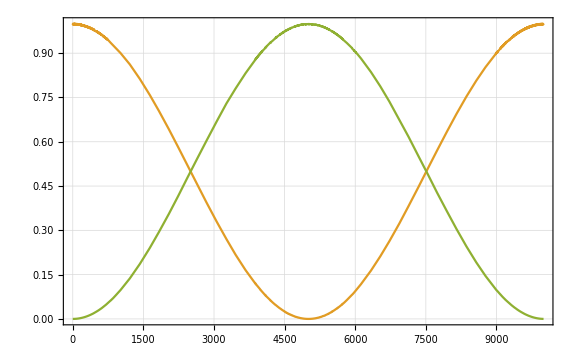
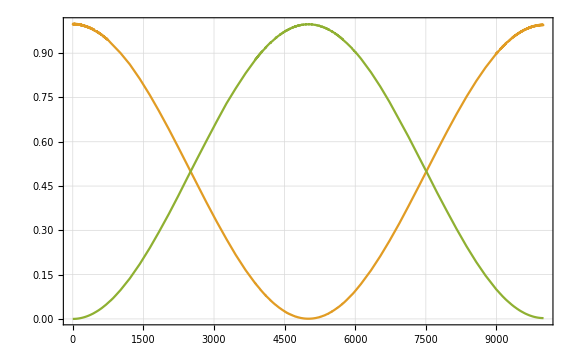
Grid[{-Graphics-,-Graphics-}]

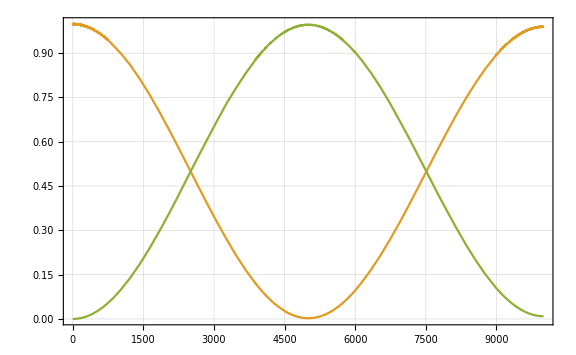
Grid[{-Graphics-,-Graphics-}]

```mathematica
ρ[10000,H,R,h1,h2,sub]
ρ[10000,H,R,h1//.approx,h2//.approx,sub]
```

```mathematica
ρ0=({{0, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
Cab[a_,b_]:=KroneckerProduct[R[[a,;;]],Transpose[Inverse[R]][[b,;;]]]*(Inverse[R].ρ0.R);
Series[Cab[2,2],{δ,∞,2}]//Normal//Simplify
En=Diagonal[Inverse[R].H.R];
Series[Ω=Table[En[[j]]-En[[k]],{j,4},{k,4}]//.{w03->0,w30->0,w33->0,dzz->0},{δ,∞,2}]//Normal//Simplify
hn1=Diagonal[Inverse[R].h1.R];
hn2=Diagonal[Inverse[R].h2.R];
Series[Γsquared=Table[hn1[[j]]-hn1[[k]],{j,4},{k,4}]^2+Table[hn2[[j]]-hn2[[k]],{j,4},{k,4}]^2//.approx,{δ,∞,2}]//Normal//Simplify
```

(0 | (gf^2 n0)/(2 δ^2) | (gf^2 n0)/(2 δ^2) | 0
(gf^2 n0)/(2 δ^2) | 1/4 | 1/4 ((gf^2 (2-4 n0))/δ^2+1) | (gf^2 (n0-1))/(2 δ^2)
(gf^2 n0)/(2 δ^2) | 1/4 ((gf^2 (2-4 n0))/δ^2+1) | (gf^2 (1-2 n0))/δ^2+1/4 | (gf^2 (n0-1))/(2 δ^2)
0 | (gf^2 (n0-1))/(2 δ^2) | (gf^2 (n0-1))/(2 δ^2) | 0)

(0 | -δ-(2 gf^2 n0)/δ | -δ-(2 gf^2 (n0+1))/δ | -(2 (δ^2+gf^2 (2 n0-1)))/δ
δ+(2 gf^2 n0)/δ | 0 | -(2 gf^2)/δ | -δ-(2 gf^2 (n0-1))/δ
δ+(2 gf^2 (n0+1))/δ | (2 gf^2)/δ | 0 | -δ-(2 gf^2 (n0-2))/δ
2 δ+(2 gf^2 (2 n0-1))/δ | δ+(2 gf^2 (n0-1))/δ | δ+(2 gf^2 (n0-2))/δ | 0)

(0 | (8 gc^2 gf^2 n0^2 wp^2)/(δ^2 dc^2) | (8 (gc gf n0 wp+gc gf wp)^2)/(δ^2 dc^2) | (8 (2 gc gf n0 wp-gc gf wp)^2)/(δ^2 dc^2)
(8 gc^2 gf^2 n0^2 wp^2)/(δ^2 dc^2) | 0 | (8 gc^2 gf^2 wp^2)/(δ^2 dc^2) | (8 gc^2 gf^2 (n0-1)^2 wp^2)/(δ^2 dc^2)
(8 (gc gf n0 wp+gc gf wp)^2)/(δ^2 dc^2) | (8 gc^2 gf^2 wp^2)/(δ^2 dc^2) | 0 | (8 (gc gf n0 wp-2 gc gf wp)^2)/(δ^2 dc^2)
(8 (2 gc gf n0 wp-gc gf wp)^2)/(δ^2 dc^2) | (8 gc^2 gf^2 (n0-1)^2 wp^2)/(δ^2 dc^2) | (8 (gc gf n0 wp-2 gc gf wp)^2)/(δ^2 dc^2) | 0)

```mathematica
J[t_]:=(2-EulerGamma-Log[2π*10^-9*t])/(2*Log[10^12])*t^2;
```

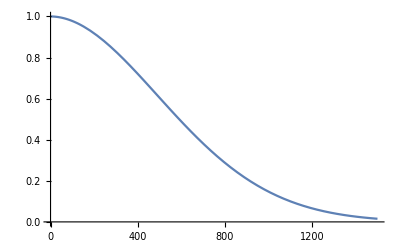

```mathematica
Plot[{Exp[-J[t]*(gc^2 wp^2 (2 √(n0-1) √n0 Sin[2ϕ]+2 n0+Cos[2ϕ]-1))/(2 dc^2)*4 π^2//.sub]},{t,0,1500}]
```

```mathematica
-(J[t]*1/2 dxy^2 (-(n0-1) Cos[2ϕ]+n0+1)^2)//.sub
```

-3.75236×10^-13 t^2 (-log((π t)/500000000)-ℽ+2)

```mathematica
(-(n0-1) cos[2ϕ]+n0+1)^2//.sub//N
```

(5.-3. cos(1.42745))^2

```mathematica
(2 √n0 √(n0-1)Sin[2ϕ]+2n0-1+Cos[2ϕ])//.ϕ-> ArcTan[√n0,√(n0-1)]//TrigExpand//Simplify
```

4 n0-2

```mathematica
-√2 gf √(n0-1) Sin[ϕ]-√2 gf √n0 Cos[ϕ]//.ϕ-> ArcTan[√n0,√(n0-1)]//TrigExpand//Simplify
```

-gf √(4 n0-2)